----------------;

Data input σ_Li/σ_Ti=0

Fits to data σ_U=σ_T+ϵσ_L

σ_T=-41.8355  σ_L=642.979  |σ_L|/|σ_T|≈ 15.3692

δσ_U=27.1061

SD=standist

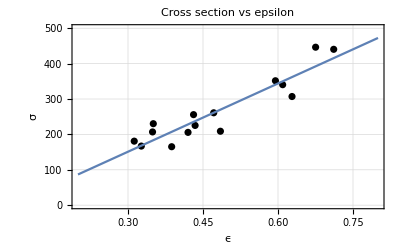

----------------;

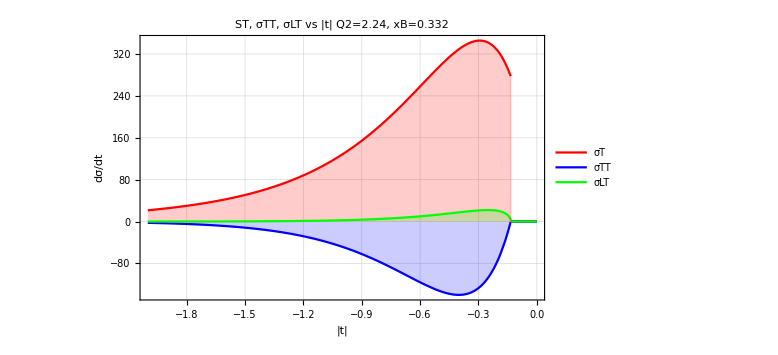

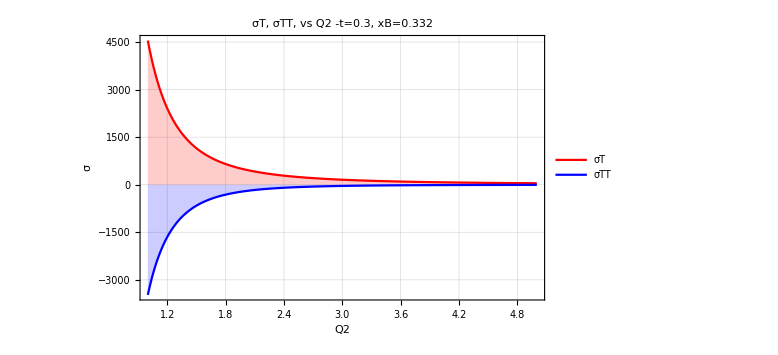

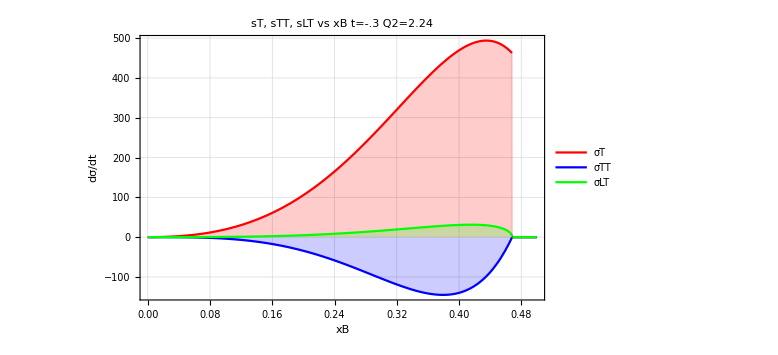

sT=If[-t>0.134112,sT0,0.]

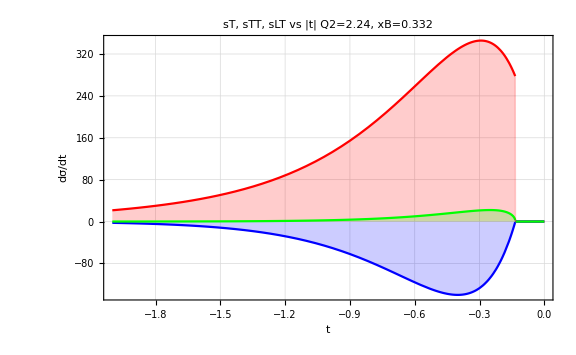

```mathematica
(*ClearAll["Global`*"]*)
(*ClearAll["`*"]*)
Clear["Global`*"]
Clear[t,xB, Q2]
mpi0    = 0.1349764 ;
mp           = 0.93827231 ;
Ebeam      = 5.75;

(*
*6.2624,0.8032,-0.1152,1.7431,0.0,
*92.9727,3.4071,-1.9099,-0.1199,0.0,16.8603,2.1722,
*)
p1=6.2059;
p2=0.8019;
p3=-0.1064;
p4=1.836;
p5=0.0;

p6=92.6402;
p7=3.4433;
p8=-1.9773;
p9=-0.1315;
p10=0.0;
p11=16.9977;
p12=2.1240;
ALPHA=0.00729927;
Hc2=389379.36;

ksi=xB/(2-xB)*(1+mp^2/Q2);
W=Sqrt[Q2*(1/xB-1)+mp^2];

E1CM=(W^2+Q2+mp^2)/(2*W);
E3CM=(W^2-mpi0^2+mp^2)/(2*W);

P1CM= √(E1CM^2-mp^2);
P3CM= √(E3CM^2-mp^2);

y=Q2/(2*mp*xB*Ebeam);
E1=Q2/(4*E^2);

tmin=-(((Q2+mpi0^2)^2)/(4 W^2)-(P1CM-P3CM)^2);



PHASE=16*Pi*(W^2-mp^2)*√(W^4+Q2^2+mp^4+2*W^2*Q2-2*W^2*mp^2+2*Q2*mp^2);

HT=p1*Q2^(p4/2.)*ⅇ^((p2+p3*(Log[xB]-Log[0.15]))*t);

ET=p6*Q2^(p9/2.)*ⅇ^((p7+p8*(Log[xB]-Log[0.15]))*t);

HTEBAR=p11*ⅇ^(p12*t);

Htildeu0=xB^-0.32*(1-xB)^3*(0.213+0.929*√xB+12.59*xB-12.57*xB^(3/2))*ⅇ^(t*((1-xB)^3*(0.432*Log[1/xB]+0.654)+xB*(1-xB)^2*1.239));
Htildeu=xB^-0.32*(1-xB)^3*(0.213+0.929*√xB+12.59*xB-12.57*xB^(3/2))*ⅇ^(t*((1-xB)^3*(0.432*Log[1/xB]+0.654)+xB*(1-xB)^2*1.239));

(*Htilded=xB^(-0.32)*(1-xB)^3*(-0.204-0.940*sqrt(xB)-0.314*xB+1.524*xB^(3/2))
exp[t*((1-xB)^3*(0.387*Ln[1/xB]+0.400)+xB*(1-xB)^2*4.284)]*)


sTT0=(-Hc2*4*Pi*ALPHA)/(2  PHASE Q2^2)*((-t-tmin)/(8 mp^2)*ET^2);
sTT=If[-t>tmin,sTT0,0.0];
sT0=  (Hc2*4*Pi*ALPHA)/(2  PHASE Q2^2)*((1-ksi^2)*HT^2+(-t-tmin)/(8 mp^2)*ET^2);
sT=If[-t>tmin,sT0,0.0];
sLT0=(Hc2*4*Pi*ALPHA)/(√2  PHASE Q2^1.5)*ksi*√(1.-ksi^2)*(√(-t-tmin))/(2 mp)HTEBAR^2;
sLT=If[-t>tmin,sLT0,0.0];

sL0=  (Hc2*4*Pi*ALPHA)/(PHASE Q2^2)*
((1.-ksi^2)*Htildeu^2-2 ksi^2 Re[Htildeu*Etilded]--t/(4 mp^2)ksi^2*Etilded^2);
(*sL=If[-t>tmin,sL0,0.0];*)

sL=0;
(*sLps=sT;*)
sU= sT+eps*sL;
(* eps1=(1-y-Q2/(4*Ebeam^2))/(1-y+y^2/2+Q2/(4*Ebeam^2)); *)

eps=(1-y-Q2/(4*Ebeam^2))/(1-y+y^2/2+Q2/(4*Ebeam^2));


Q2List={  1.14,  1.38,   1.61,  1.75,  1.87,   1.95,    2.1,  2.21,   2.24,  2.34,  2.71,  2.75,  3.12,   3.23,   3.29,  3.68,  3.76,4.230};
xBList={ 0.131,0.169,0.186,0.223,0.270,0.313,0.238,0.275,0.332,0.403,0.336,0.423,0.362,0.428,0.496,0.451,0.513,0.539};
Clear[xB,Q2];
epslist={};
sUlist={};
t=-0.35;
" ----------------;"
Clear[Q2, xB]
epssUlist={};
imax=0;
Do[
xB=xBList[[i]];Q2=Q2List[[i]];
If[-t-tmin>0,{imax=imax+1,epslist=Append[epslist,eps], sUlist=Append[sUlist,{eps,sU}]}];
(*Print["i=",i,"  xB=",xB,"  Q2=",Q2,"  eps=",eps,"  sU=",sU];*)
,{i,1,18}]

sUfit=NonlinearModelFit[sUlist,sTfit0+ epsilon sLfit0,{sTfit0,sLfit0},epsilon];
variance=sUfit["EstimatedVariance",VarianceEstimatorFunction->(Mean[Abs[#]]&)];
sTfit=sTfit0/.sUfit["BestFitParameters"];
sLfit=sLfit0/.sUfit["BestFitParameters"];
Print[" Data input σ_Li/σ_Ti=0 " ]
Print["Fits to data σ_U=σ_T+ϵσ_L" ]
Print["σ_T=",sTfit, "  σ_L=",sLfit, "  |σ_L|/|σ_T|≈ ",Abs[sLfit]/Abs[sTfit]]
Print["δσ_U=",variance]
Print["SD=",standist]
Show[ListPlot[sUlist,PlotStyle->{Black},
Frame->True,
FrameLabel->{"ϵ","σ"},
PlotStyle->{Directive[lineStyle]},FrameLabel->{"ϵ","σ"},PlotLabel->"Cross section vs epsilon",
GridLines->Automatic,PlotRange->{{0.2,0.8},{0.,500.}}],Plot[sUfit[epsilon1],{epsilon1,.2,.8}]]
" ----------------;"


Clear[t];
Q2= 2.24;xB=.332;

Plot[{sT,sTT,sLT},{t,-0,-2.},
PlotLabel->"ST, σTT, σLT vs |t|           Q2=2.24, xB=0.332",
PlotStyle->{Red,Blue,Green},
Frame->True,Filling->Axis,
FrameLabel->{"|t|","dσ/dt"},
PlotStyle->{Directive[lineStyle]},
ImageSize->Large,BaseStyle->{FontSize->16},
GridLines->Automatic,
PlotRange->{{-0,-2.},{-200,400.}},
PlotLegends->Placed[{"σT","σTT","σLT"},Right]
]
Clear[Q2];t=-0.3;xB=0.332;
Plot[{sT,sTT},{Q2,1.,5.},
PlotLabel->" σT, σTT, vs Q2          -t=0.3, xB=0.332",
PlotStyle->{Red,Blue,Green},
Frame->True,Filling->Axis,
FrameLabel->{"Q2","σ"},
PlotStyle->{Directive[lineStyle]},
ImageSize->Large,BaseStyle->{FontSize->16},
GridLines->Automatic,
PlotRange->{{1.,5.},All},
PlotLegends->Placed[{"σT","σTT"},Right]
]

Clear[xB];t=-.3;Q2= 2.24;

Plot[{sT,sTT,sLT},{xB,0.0,0.5},
PlotLabel->"sT, sTT, sLT vs xB           t=-.3  Q2=2.24",
PlotStyle->{Red,Blue,Green},
Frame->True,Filling->Axis,
FrameLabel->{"xB","dσ/dt"},
PlotStyle->{Directive[lineStyle]},
ImageSize->Large,BaseStyle->{FontSize->16},
GridLines->Automatic,
PlotRange->{{0,.5},All},
PlotLegends->Placed[{"σT","σTT","σLT"},Right]
]

Clear[t]
xB=0.332;Q2= 2.24;
Print["sT=",sT]
Plot[{sT,sTT,sLT},{t,0.,-2.},
PlotLabel->"sT, sTT, sLT vs |t|           Q2=2.24, xB=0.332",
PlotStyle->{Red,Blue,Green},
Frame->True,Filling->Axis,
FrameLabel->{"t","dσ/dt"},
PlotStyle->{Directive[lineStyle]},
ImageSize->Large,BaseStyle->{FontSize->16},
GridLines->Automatic,
PlotRange->{{0,-2.0},{-200,400.}}
]
```